# XXZ model with NNN interaction

Parameters of the Hamiltonian

*) L = number of sites.                                                                                                                                                         *) upspins = number of spins pointing up in the z direction.
*) downspins = number of spins pointing down in the z direction.
*) dim = dimension of the Sz-subspace considered.
*) ϵ= value of the defect (all other Zeeman splittings are assumed = 0).
*) defectsite = site where the defect is placed.
*) Jxy = strength of the flip-flop term between nearest-neighbors (NNs).
*) Jz = strength of the Ising interaction between NNs.
*) alpha different from zero indicates the presence of next-nearest-neighbor (NNN) couplings.
*) JJxy = strength of the flip-flop term between NNNs.
*) JJz = strength of the Ising interaction between NNNs.
*) onebasisvector is the site-basis vector 111110000000000
*) its permutations generate all basis vectors for that particular subspace
*) HH are the elements of the Hamiltonian. In the site-basis, the on-site defect and the Ising interaction contribute to
the diagonal elements. The flip-flop term contributes to the off-diagonal elements.

Magnetization of each site

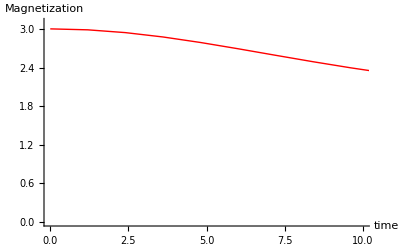

```mathematica
(*PARAMETERS OF THE HAMILTONIAN*)
Clear[L,upspins,downspins,dim,Jxy,Jz,ϵ,defectsite,alpha,JJxy,JJz];
L=12;
upspins=L/2;
downspins=L-upspins;
dim=L!/(upspins! downspins!);
(*Impurity*)
ϵ=0.0;
defectsite=Floor[L/2];

(*Parameters for nearest-neighbor couplings*)
Jxy=1.0;
  Jz=0;
(*Parameters for next-nearest-neighbor couplings*)
(*Set alpha=0 if NNN couplings do not exist*)
alpha=0.5;
JJxy=1.0;
JJz=0;

(*BASIS*)
Clear[onebasisvector,basis];
onebasisvector=Flatten[{Table[1,{k,1,upspins}],Table[0,{k,1,downspins}]}];
basis=Permutations[onebasisvector];

(* ELEMENTS OF THE HAMILTONIAN *)
(* Impurity and NN couplings *)

Clear[HH];
(* Initialization *)
Do[Do[HH[i,j]=0.,{i,1,dim}],{j,1,dim}];

(* Diagonal elements *)
Do[
(* Impurity *)
If[basis[[i,defectsite]]==1, HH[i,i]=HH[i,i] + ϵ/2.,  HH[i,i]=HH[i,i] - ϵ/2.];
(* Ising interaction *)
Do[If[basis[[i,j]]==basis[[i,j+1]],HH[i,i]=HH[i,i]+Jz/4.,HH[i,i]=HH[i,i]-Jz/4.];
,{j,1,L-1}];
(* CLOSED chain *)
(*If[basis[[i,1]]==basis[[i,L]],HH[i,i]=HH[i,i]+Jz/4.,HH[i,i]=HH[i,i]-Jz/4.];*)
,{i,1,dim}];

(* Off-diagonal elements *)
Clear[howmany,site];
Do[
Do[
(* Initialization *)
howmany=0;
Do[site[kk] = 0, {kk,1, L}];
(* Sites where states i and j differ *)
Do[ If[basis[[i,k]]≠basis[[j,k]], {howmany=howmany+1, site[howmany]=k}];
,{k,1,L}];
(* If only two neighbor sites differ, there is a coupling matrix element *)
If[howmany == 2, 
If[site[2] - site[1]==1, {HH[i,j]=Jxy/2.,HH[j,i]=Jxy/2.}]];
(* CLOSED chain *)
(*If[howmany == 2, If[site[2] - site[1]==L-1, {HH[i,j]=Jxy/2.,HH[j,i]=Jxy/2.}]];*)
,{j,i+1,dim}];
,{i,1,dim-1}];

(*ELEMENTS OF THE HAMILTONIAN WITH NNN COUPLINGS*)
If[alpha>0,
(*Diagonal elements*)
Do[
(*Ising interaction*)
Do[If[basis[[i,j]]-basis[[i,j+2]],
HH[i,i]=HH[i,i]+alpha*JJz/4.,HH[i,i]=HH[i,i]-alpha*JJz/4.];
,{j,1,L-2}];
,{i,1,dim}];
(*Off-diagonal elements*)
Clear[howmany,site];
Do[
Do[
(*Initialization*)
howmany=0;
Do[site[kk]=0,{kk,1,L}];
(*Sites where states i and j differ*)
Do[
If[basis[[i,k]]≠basis[[j,k]],{howmany=howmany+1,site[howmany]=k}];,
{k,1,L}];
(*If only two next-neighbor sites differ,there is a coupling matrix element*)If[howmany==2,If[site[2]-site[1]==2,{HH[i,j]=alpha*JJxy/2.,HH[j,i]=alpha*JJxy/2.}]];
,{j,i+1,dim}];
,{i,1,dim-1}];];

(* TOTAL HAMILTONIAN AND DIAGONALIZATION *)
Clear[Hamiltonian,Energy,Vector];
Hamiltonian=Table[Table[HH[i,j],{j,1,dim}],{i,dim}];
Energy=Eigenvalues[Hamiltonian];
Vector=Eigenvectors[Hamiltonian];

(*Choose an initial state*)
(*Do[
If[basis[[i,1]]*basis[[i,2]]==1 && basis[[i,2]]*basis[[i,3]]==1,initialstate=i];
,{i,1,dim}];*)
initialstate=1;

(*DYNAMICS*)
Clear[endtime,PSI,increment,Magsite];
endtime=51;
increment=.2;
Do[PSI[t]=Sum[Vector[[j,initialstate]]Vector[[j]] Exp[-I Energy[[j]](t-1) increment],{j,1,dim}];
(*Magnetization*)
Do[Magsite[j,t]=0.5 Sum[Abs[PSI[t][[i]]]^2(-1.)^(1+basis[[i,j]]),{i,dim}];
,{j,1,L}];
(*Print[{(t-1)increment,Magsite[1,t]}];*)
,{t,1,endtime}];


(*Call Package for Legends*)
<<PlotLegends`
Clear[magT];

Do[magT[j]=Table[{(t-1) increment,Magsite[j,t]},{t,1,endtime}],{j,1,L/2}];
delta00=Sum[magT[j],{j,1,L/2}];

Print[];
Print["Magnetization of each site"];
ListPlot[delta00,PlotRange->{{0,10},{0,3.1}},Joined->True,PlotStyle->{{Thick,Red} },LabelStyle->Directive[Black,Bold,Medium],PlotLegend->{"Δ=0.0"},LegendPosition->{1,0},AxesLabel->{"time","Magnetization"}]
```

# Plot three figure together

```mathematica
ListPlot[{delta00,delta05,delta10},PlotRange->{{0,30},{0,3.1}},Joined->True,PlotStyle->{{Thick,Black}, {Thick,Red},{Thick,Green}},LabelStyle->Directive[Black,Bold,Medium],PlotLegend->{"Δ=0.0","Δ=0.5","Δ=1.0"},LegendPosition->{1,0},AxesLabel->{"time","Magnetization"}]
```